```mathematica
Clear["Global`*"]
```

```mathematica
M:=8.4 10^(-3)
p:=4
μ:=100
ϕ0:=89.6237
ϕend:=99.3003
V[t_]:=M^4 (1-(ϕ[t]/μ)^p)
Vp[t_]=D[V[t],ϕ[t]];
(*ϕsr,asr*)
sol=NDSolve[{ 3 a'[t]/a[t] ϕ'[t]+Vp[t]==0,
a'[t]==a[t]Sqrt[1/3 (V[t])], 
ϕ[0]==ϕ0,a[0]==1},{ϕ,a},
{t,0,6.5 10^3}];
asr[t_]:=(a/.First[sol])[t]
ϕsr[t_]:=(ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
(*ϕ,a*)
sol1=NDSolve[{ϕ''[t]+ 3 a'[t]/a[t] ϕ'[t]+Vp[t]==0,
a'[t]==a[t]Sqrt[1/3 (1/2 ϕ'[t]^2+V[t])], 
ϕ[0]==ϕsr[0],ϕ'[0]==ϕsrp[0],a[0]==asr[0]},{ϕ,a},
{t,0,6.5 10^3}];
aex[t_]:=(a/.First[sol1])[t]
aexpp[t_]=D[aex[t],{t,2}];
ϕex[t_]:=(ϕ/.First[sol1])[t]
fun[t_]:=aexpp[t]/aex[t]
```

```mathematica
asr[650]
```

1.0159

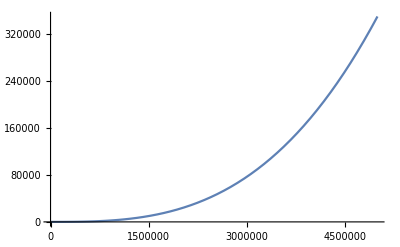

```mathematica
Plot[aex[t],{t,0,5 10^6}]
```

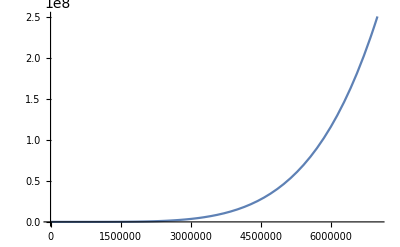

```mathematica
Plot[ϕex[t],{t,10,7 10^6}]
```